# The Perron-Frobenius Theorem, Population Modeling, and Bipartite Graphs

I verify the Bipartite graph theorem on a couple of examples, then I show how Perron-Frobenius theorem can be used in conjunction with a Leslie matrix to gain information about the long-term age-distribution of a population.

James Pedersen, Jun. 30,  2018

According to theorems 4 and 6 in:

```mathematica
Hyperlink["https://people.orie.cornell.edu/dpw/orie6334/lecture3.pdf"]
```

https://people.orie.cornell.edu/dpw/orie6334/lecture3.pdf

if G is a connected undirected graph G with adjacency matrix A and λ_1≥    ... ≥ λ_n are the eigenvalues of A, G is bipartite iff λ_n=-λ_1. This is the bipartite graph theorem. It is related to something called the Perron-Frobenius theorem, which states that (according to Wikipedia), if A is an n x n matrix with all nonnegative entries, then

There exists an eigenvector r of A with nonnegative components such that if λ is any eigenvector of A then |λ| ≤ |r|.

A has an eigenvector x with eigenvalue λ where all components of x are nonnegative.

## Examples of the Bipartite Graph Theorem:

Consider the graph

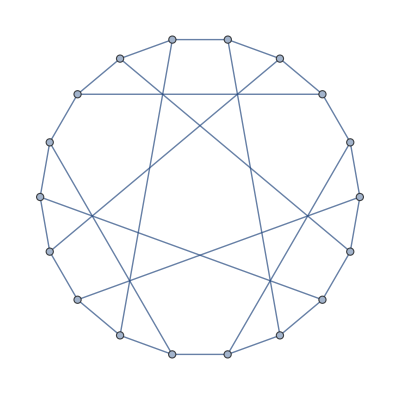

```mathematica
g=GraphData["PappusGraph"]
```

g is a connected graph:

```mathematica
ConnectedGraphQ[g]
```

True

Sorting the eigenvalues of g in ascending order,

```mathematica
Sort[Eigenvalues[AdjacencyMatrix[g]],Less]
```

{-3,-√3,-√3,-√3,-√3,-√3,-√3,0,0,0,0,√3,√3,√3,√3,√3,√3,3}

we see that -(-3) = 3, so g must be bipartite.

```mathematica
BipartiteGraphQ[g]
```

True

In fact, Mathematica’s graph embedding tools make it easy to for one to see that g is bipartite:

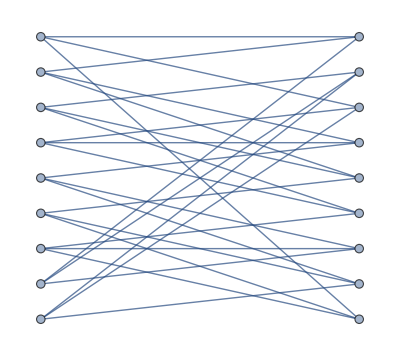

```mathematica
Graph[VertexList[g],EdgeList[g],GraphLayout->"BipartiteEmbedding"]
```

What about a negative example? Consider the following graph:

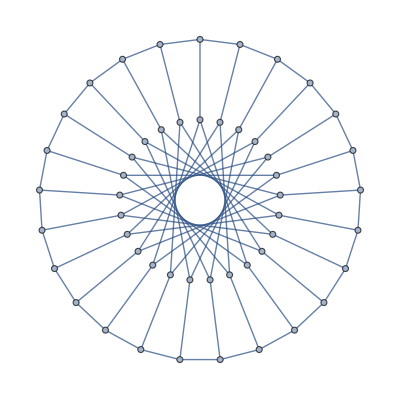

```mathematica
g=PetersenGraph[25,15]
```

```mathematica
Sort[N[Eigenvalues[AdjacencyMatrix[g]]], Less]
```

{-2.74606,-2.74606,-2.46106,-2.46106,-2.32412,-2.32412,-2.07289,-2.07289,-1.94908,-1.94908,-1.88001,-1.88001,-1.87603,-1.87603,-1.3577,-1.3577,-0.994792,-0.994792,-0.731528,-0.731528,-0.431826,-0.431826,-0.0466154,-0.0466154,0.0356204,0.0356204,0.0935099,0.0935099,0.580442,0.580442,0.957921,0.957921,1.,1.12418,1.12418,1.23806,1.23806,1.4027,1.4027,2.12259,2.12259,2.19914,2.19914,2.258,2.258,2.33503,2.33503,2.52452,2.52452,3.}

Here -2.74606 is not equal to -3, so g cannot be bipartite.

```mathematica
BipartiteGraphQ[g]
```

False

Note that attempting to visualize g as a bipartite graph fails, as expected:

```mathematica
Graph[VertexList[g],EdgeList[g],GraphLayout->"BipartiteEmbedding"]
```

One more large example, creating a large undirected graph directly from a random 50x50 adjacency matrix:

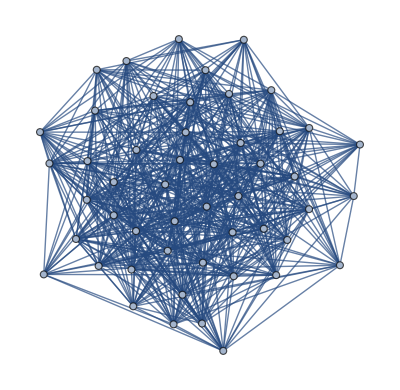

```mathematica
B=50;
A=Table[Table[If[k<l,RandomInteger[1],0],{l,1,B}],{k,1,B}];
B=Transpose[A];
adjmatrix=A+B;
Dimensions[adjmatrix];
SymmetricMatrixQ[adjmatrix];
g=UndirectedGraph[AdjacencyGraph[adjmatrix]]
```

Odds are that g will be connected yet not bipartite:

```mathematica
ConnectedGraphQ[g]
BipartiteGraphQ[g]
list=N[Sort[Eigenvalues[adjmatrix],Less]]
```

True

False

{-7.13749,-6.23377,-5.69327,-5.48302,-5.25683,-4.90149,-4.8475,-4.51198,-4.15107,-3.85244,-3.67306,-3.38214,-3.29365,-3.08944,-2.91825,-2.81661,-2.49561,-2.28344,-2.00102,-1.56365,-1.44728,-1.34024,-1.23216,-0.84555,-0.399136,-0.225044,-0.0583955,0.150549,0.246833,0.595835,0.790193,0.872142,0.958683,1.50826,1.66746,2.06423,2.22938,2.28126,2.65021,3.0903,3.44125,3.51978,3.66745,3.96047,4.39964,5.05651,5.20615,5.63461,5.89507,25.2473}

## Application of the Perron-Frobenius Theorem to Population Modeling:

How will the American mink population of Great Britain evolve over time? In

```mathematica
Hyperlink["https://en.wikipedia.org/wiki/American_mink"]
```

https://en.wikipedia.org/wiki/American_mink

Wikipedia writes that "The total mink population in Great Britain is estimated at 110,000 (England; 46,750, Scotland; 52,250, Wales; 9,750)". The article:

```mathematica
Hyperlink["https://onlinelibrary.wiley.com/doi/abs/10.1111/j.1365-2907.2006.00079.x"]
```

https://onlinelibrary.wiley.com/doi/abs/10.1111/j.1365-2907.2006.00079.x

boasts the following data tables:

The authors have grouped the data into seven age categories (the first two categories being “Juveniles” and “Subadults”). Now consider only the data for South Harris. Is the sample of South-Harris minks whose data is listed in the above table representative of the current population of minks in Great Britain? Without a doubt, a correction must be made for human interference. This is because the (human) population of South Harris (which is a part of the island of Lewis and Harris in Scotland) is much smaller than the (human) population of Great Britain.

```mathematica
EntityValue[Interpreter["Island"]["lewis and harris"],"Population"]
EntityValue[Interpreter["Country"]["Great britain"],"Population"]
```

21031 people

65397080 people

We may (at least partially) correct for this by assuming that for each age class x there is a constant k_x< 1 such that the true survival rate of American minks in Britain from age class x to age class x+1 is the rate listed in the table times k_x. Furthermore, the authors write that “The youngest individual caught in our study was almost 3 months old; therefore, the data do not include kits (defined as individuals less than 3 months of age and usually still with their mothers, cf. Yamaguchi & Macdonald, 2003).” Thus we must limit our scope of inference accordingly. Apart from these adjustments, simplicity’s sake assume that the sample of South Harris minks described in the above table is indeed representative of the current population of American minks (aside from kits) in Great Britain.

The goal is to understand how the population of American minks (aside from kits) in Great Britain will evolve over time. This may be done using something called a Leslie matrix. The Wikipedia article about Leslie matrices states that they have the following form:

where n_k is the number of members of the population in age class k (at some time), s_x is the fraction of individuals of the population that survive from age class x to age class x+1, and f_x= s_x b_(x+1) is the fecundity, where b_xis the per-capita birth rate of minks in age class x.

We have enough data to explicitly compute the Leslie matrix for our population (the current population of American minks in Great Britain that are not kits will henceforth be referred to as “our population”). First we must fetch some data:

```mathematica
ResourceObject["Amniote Life History EntityStore"];
ResourceData["Amniote Life History EntityStore"];
PrependTo[$EntityStores,ResourceData["Amniote Life History EntityStore"]]
```

{EntityStore[<|Types -> <|Amniote -> <|Entities -> <|ChloroceryleAenea -> <|class -> Aves, order -> Coraciiformes, family -> Alcedinidae, genus -> Chloroceryle, species -> aenea, subspecies -> Null, common_name -> America<<13>>isher, <<27>>, no_sex_svl_cm -> Missing[NoInput], no_sex_maturity_d -> Missing[NoInput], Label -> American Pygmy Kingfisher|>, <<499>>|>, <<1>>|>|>|>],EntityStore[<|Types -> <|Amniote -> <|Entities -> <|ChloroceryleAenea -> <|class -> Aves, order -> Coraciiformes, family -> Alcedinidae, genus -> Chloroceryle, species -> aenea, subspecies -> Null, common_name -> America<<13>>isher, <<27>>, no_sex_svl_cm -> Missing[NoInput], no_sex_maturity_d -> Missing[NoInput], Label -> American Pygmy Kingfisher|>, <<499>>|>, <<1>>|>|>|>]}

Let us compute the class to class survival rates s_x.

```mathematica
Clear[k1];Clear[k2];Clear[k3];Clear[k4];Clear[k5];Clear[k6];Clear[k7];
s=Times@@{{k1 ,k2,k3,k4,k5,k6,k7},{25/72,21/25,4/21,3/4,3/3,0/3,0}}
```

{(25 k1)/72,(21 k2)/25,(4 k3)/21,(3 k4)/4,k5,0,0}

Now let us compute the fecundity values:

```mathematica
americanmink=EntityClass["Amniote","species"->"vison"]
```

```mathematica
EntityProperties[americanmink]
```

{adult body mass g,adult svl cm,birth or hatching svl cm,birth or hatching weight g,class,common name,egg length mm,egg mass g,egg width mm,family,female body mass at maturity g,female body mass g,female maturity d,female svl at maturity cm,female svl cm,fledging age d,fledging mass g,genus,gestation d,incubation d,inter litter or interbirth interval y,Label,litter or clutch size n,litters or clutches per y,longevity y,male body mass g,male maturity d,male svl cm,maximum longevity y,no sex body mass g,no sex maturity d,no sex svl cm,order,species,subspecies,weaning d,weaning weight g}

```mathematica
{litersperyear,littersize}=Flatten[EntityValue[americanmink,{"inter_litter_or_interbirth_interval_y","litter_or_clutch_size_n"}]]
```

{0.999316 yr,4.76}

```mathematica
numclasses=7;
percapitabirthrateperageclass=QuantityMagnitude/@Prepend[ConstantArray[litersperyear * littersize,numclasses-1],litersperyear  * littersize / 2]/2
fecundities=Times@@{s,percapitabirthrateperageclass}
```

{1.18919,2.37837,2.37837,2.37837,2.37837,2.37837,2.37837}

{0.412912 k1,1.99783 k2,0.453023 k3,1.78378 k4,2.37837 k5,0.,0.}

Only some of the minks in age class 1 (the subadult age class) will reproduce in any given year, because “Sexual maturity is attained during the kit’s first spring, when they are about 10 months old”, according to pages 663-664 of the following book:

```mathematica
Hyperlink["https://books.google.com/books?id=-xQalfqP7BcC&printsec=frontcover#v=onepage&q&f=false"]
```

https://books.google.com/books?id=-xQalfqP7BcC&printsec=frontcover#v=onepage&q&f=false

and also because the authors of the paper “define a juvenile mink as one between 3 months and 6 months of age, a subadult as between 7 months and 1 year, and an adult as 1 year or older”.

We have sufficient data to compute the Leslie matrix for our population:

```mathematica
L=Join[{fecundities},Table[Table[If[j==i,s[[j+1]],0],{j,0,w-1}],{i,0,w-2}]];
MatrixForm[L]
```

(0.412912 k1 | 1.99783 k2 | 0.453023 k3 | 1.78378 k4 | 2.37837 k5 | 0. | 0.
(25 k1)/72 | 0 | 0 | 0 | 0 | 0 | 0
0 | (21 k2)/25 | 0 | 0 | 0 | 0 | 0
0 | 0 | (4 k3)/21 | 0 | 0 | 0 | 0
0 | 0 | 0 | (3 k4)/4 | 0 | 0 | 0
0 | 0 | 0 | 0 | k5 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0)

Suppose that

```mathematica
k1=k2=k3=k4=k5=k6=k7=3/4
```

3/4

We can use the Leslie matrix to compute the number of minks in our population after, say, 5 years, 10 years, and 15 years:

```mathematica
initialpopulation=110000;
agescountinsample={72,25,21,4,3,3,0};
samplesize=Total[agescountinsample];
initialpopulationbyages=Floor[initialpopulation*agescountinsample/samplesize]
Nest[L.#&,initialpopulationbyages,5]
Nest[L.#&,initialpopulationbyages,10]
Nest[L.#&,initialpopulationbyages,15]
```

{61875,21484,18046,3437,2578,2578,0}

{41151.7,11897.9,8543.33,1319.3,879.094,611.801,0.}

{23659.7,6880.03,4843.19,772.487,485.254,406.896,0.}

{13610.8,3958.87,2785.65,444.485,279.235,233.94,0.}

Consider the eigenvalues of L. The Perron-Frobenius theorem guarantees that L has a "leading eigenvalue", an eigenvalue with nonnegative components greater than or equal in norm to every other eigenvalue of L.

```mathematica
sortedeigenvalues=Sort[Eigenvalues[L],If[Norm[#1]<Norm[#2],1,If[Norm[#1]>Norm[#2],-1],0]&]
Norm/@sortedeigenvalues
```

{0.+0. ⅈ,0.+0. ⅈ,0.104573+0.210822 ⅈ,0.104573-0.210822 ⅈ,-0.248078+0. ⅈ,-0.579669+0. ⅈ,1.02078+0. ⅈ}

{0.,0.,0.235333,0.235333,0.248078,0.579669,1.02078}

```mathematica
r=Last[sortedeigenvalues]
```

1.02078+0. ⅈ

r is the largest eigenvalue of L. The Perron-Frobenius theorem also states that L has an eigenvector x corresponding to r with all nonnegative components. In the below computation, note that -v is an eigenvector if v is an eigenvector.

```mathematica
Eigenvectors[L]
```

{{-0.924706+0. ⅈ,-0.306366+0. ⅈ,-0.22589+0. ⅈ,-0.00396219+0. ⅈ,-0.00291116+0. ⅈ,-0.00285191+0. ⅈ,0.+0. ⅈ},{0.721986+0. ⅈ,-0.421226+0. ⅈ,0.546919+0. ⅈ,-0.0168932+0. ⅈ,0.0218571+0. ⅈ,-0.0377062+0. ⅈ,0.+0. ⅈ},{-0.171241+0. ⅈ,0.233446+0. ⅈ,-0.708249+0. ⅈ,0.0511172+0. ⅈ,-0.15454+0. ⅈ,0.62295+0. ⅈ,0.+0. ⅈ},{0.107433-0.0964394 ⅈ,-0.0555512-0.199896 ⅈ,-0.651668-0.124926 ⅈ,-0.0305466+0.0401931 ⅈ,0.0714935+0.144132 ⅈ,0.683668+0. ⅈ,0.+0. ⅈ},{0.107433+0.0964394 ⅈ,-0.0555512+0.199896 ⅈ,-0.651668+0.124926 ⅈ,-0.0305466-0.0401931 ⅈ,0.0714935-0.144132 ⅈ,0.683668+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,1.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,1.+0. ⅈ}}

```mathematica
x=Abs[First[Eigenvectors[L]]]
```

{0.924706,0.306366,0.22589,0.00396219,0.00291116,0.00285191,0.}

```mathematica
Equal[L.x,r*x]
```

True

According to Leslie’s model, x corresponds to the the stationary distribution (the distribution of the population in each age class after L has been applied infinitely many times) of the population. Furthermore, once the stationary distribution for the population is achieved, the population will grow exponentially at rate r. We can verify this empirically: After 1000 years, our population will look like:

```mathematica
endstatepopulationvector=Nest[L.#&,initialpopulationbyages,1000]
```

{6.22837×10^13,2.06353×10^13,1.52148×10^13,2.66874×10^11,1.96082×10^11,1.92091×10^11,0.}

This corresponds to the stationary distribution

```mathematica
stationarydistribution=endstatepopulationvector/Total[endstatepopulationvector]
```

{0.630473,0.208883,0.154014,0.00270146,0.00198486,0.00194446,0.}

which is practically identical to:

```mathematica
x/Total[x]
```

{0.638616,0.185749,0.130703,0.0208547,0.0131022,0.0109755,0.}

This shows how the Leslie matrix can be used to infer long-term age-distribution of a population over time.

Below is a visualization showing how the evolution over a given number of years of the population of American minks (not kits) in Great Britain depends on the k_xs (k_x= 1 - [the fraction of minks in age class x that are killed off due to human interference]). Each line shows the time-evolution of a given age class of the population (the previous cells need to be run for this to work):

```mathematica
Manipulate[With[{
s=Times@@{{k1 ,k2,k3,k4,k5,k6,k7},{25/72,21/25,4/21,3/4,3/3,0/3,0}}},
fecundities=Times@@{s,percapitabirthrateperageclass};
L=Join[{fecundities},Table[Table[If[j==i,s[[j+1]],0],{j,0,w-1}],{i,0,w-2}]];ListLinePlot[Transpose[NestList[L.#&,initialpopulationbyages,years]],PlotRange->All]],{{years,15},ControlType->"InputForm"},{{k1,3/4},0,1},{{k2,3/4},0,1},{{k3,3/4},0,1},{{k4,3/4},0,1},{{k5,3/4},0,1},{{k6,3/4},0,1},{{k7,3/4},0,1} ]
```